## Analysis of the metapopulation dynamics

#### This document includes:

Code to generate metapopulation dynamics in Figure 3A

Code to generate niche shadow plots in Figures 3B, 5C and D, S4

## Functions

```mathematica
(* copied from 1-in-patch-model.nb *)
Clear[GenerateSidModel];
GenerateSidModel[N_]:=(
Flatten[{
(* biomass: growth - washout *)
Table[M[i]'[t]==(1-α[i])γ*HoloFlux[Holo[t]]*M[i][t]-d*M[i][t]
,{i,1,N}],
(* Apo: production + recycling - chelation - washout  *)
Apo'[t]==Sum[M[j][t]*(α[j]*ϵ+HoloFlux[Holo[t]]*ρ),{j,N}]
-Chelation[Apo[t],Fe[t]]-d*Apo[t],
(* Holo: chelation - uptake - washout  *)
Holo'[t]==Chelation[Apo[t],Fe[t]]-HoloFlux[Holo[t]]*(Sum[M[j][t],{j,N}])-d*Holo[t],
(* Fe: supply - chelation - washout *)
Fe'[t]==feIn-Chelation[Apo[t],Fe[t]]-d*Fe[t]
}]
);

Clear[Chelation,HoloFlux];
Chelation[apo_,fe_]:=kf*apo*fe;
HoloFlux[holo_]:= vh*holo/(Kh+holo);

(* Default parameters *)
Clear[defaults];
defaults={
feIn->1,
d->1,

kf->1,
γ->10.,
vh->1,Kh->0.1,
vp->1,Kp->1,
ϵ->2.,
ρ->1.
};

(* Prep to solve the ODEs *)
odes=GenerateSidModel[1];
eqs=Map[0==Last[#]&,odes]/.α[1]->α/.Map[#[t]->#&,{M[1],Apo,Holo,Fe}];

Off[Solve::ratnz];
Clear[eqSol];
eqSol=Solve[eqs/.defaults,{M[1],Apo,Holo,Fe},PositiveReals][[2]];

(* Calculates the equilibrium biomass of a given α value *)
Clear[Biomass];
Biomass[None]=0;
Biomass[{α->0.}]=0;
Biomass[{α->1.}]=0;
Biomass[strain_]:=Biomass[strain]=M[1]/.eqSol/.strain/.{Undefined->0}

(* Pre-calculate biomass for landmark α values *)
alphahat=Module[{x},(x/.FindMaximum[{M[1]/.eqSol/.α->x,0<x<=0.5},x][[2]])];
alphamin=eqSol[[1]][[2]][[2]][[1]];
alphamax=eqSol[[1]][[2]][[2]][[5]];

(* Given an equilibrium biomass, back-calculate the corresponding α value. high = True finds the one >α̂ *)
Clear[Strategy];
Strategy[bio_,high_:False]:=Strategy[bio,high]=Module[{x},(
cond=If[high,x>=alphahat,x<=alphahat];
val=SolveValues[{bio==M[1]/.eqSol/.α->x,cond},{x}];
If[val=={},None,val[[1]][[1]]]
)]
```

```mathematica
(* Generate ODEs for Hastings' formulation of Levins-Culver metapopulation model *)
Clear[GenerateLevins];
GenerateLevins[N_]:=(
Clear[c,p,m];
Table[p[i]'[t] == c[i]*p[i][t]*(1-Sum[p[j][t],{j,i}])-m*p[i][t]-p[i][t]*Sum[c[j]*p[j][t],{j,i-1}],
{i,1,N}])

(* Numerically solve the Levins model for given dispersals, mortality rate, and initial values *)
Clear[SolveLevins];
SolveLevins[dispersals_,mort_,start_:0.1,maxT_:1000]:=Module[
{
size=Length[dispersals],
starts,
endT=maxT,
sol
},
Clear[c,p,m];
starts=If[NumericQ[start],ConstantArray[start,size],start];
If[size!=Length[starts],Print["Vectors are of unequal size!"];Abort[]];
sol=NDSolve[{
GenerateLevins[size] ,
Thread[Array[p[#][0]&,size]==starts]}
/.Thread[Array[c,size]->dispersals]/.m->mort ,
Array[p,size],{t,0,maxT}
];
Association[Append[sol[[1]],"end"->endT]]
];
```

## Representative dynamics (Figure 3)

```mathematica
mortality=0.5;
```

```mathematica
biomassHat=Biomass[α->alphahat]
```

5.35138

```mathematica
sol1=SolveLevins[{biomassHat}, mortality, 0.001];
```

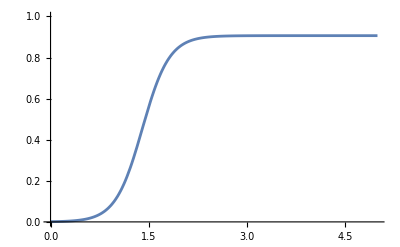

```mathematica
Plot[Evaluate[p[1][t]/.sol1], {t,0,5},PlotRange->{0,1}]
```

```mathematica
hatEq=p[1][5]/.sol1
```

0.906566

```mathematica
biomassMin=Biomass[α->alphamin+0.000001]
```

1.23967

```mathematica
sol2=SolveLevins[{biomassMin,biomassHat},mortality,{0.001,hatEq}];
```

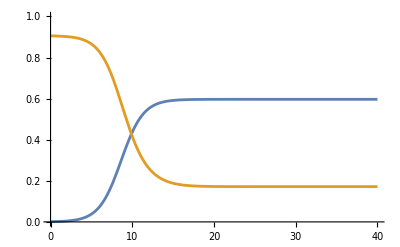

```mathematica
Plot[Evaluate[{p[1][t],p[2][t]}/.sol2], {t,0,40},PlotRange->{0,1}]
```

```mathematica
minEq=p[1][45]/.sol2
hatEq=p[2][45]/.sol2
```

0.596665

0.171681

```mathematica
biomassMid=Biomass[α->0.2]
```

5.31468

```mathematica
sol3=SolveLevins[{biomassMin,biomassMid,biomassHat},mortality,{minEq,0.001,hatEq}];
```

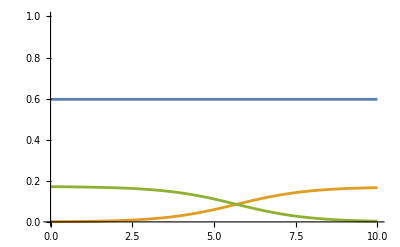

```mathematica
Plot[Evaluate[{p[1][t],p[2][t],p[3][t]}/.sol3], {t,0,10},PlotRange->{0,1}]
```

```mathematica
vars={p[1],p[2],p[3]};
t1=0; t2=t1+10; t3=t2+25;tend=t3+15;
combo[t]={
Piecewise[{
{p[1][t]/.sol1, t<=t2},
{p[2][t-t2]/.sol2,t2<t<=t3},
{p[3][t-t3]/.sol3,t3<t}
}],
Piecewise[{
{None[t], t<=t2},
{p[1][t-t2]/.sol2,t2<t<=t3},
{p[1][t-t3]/.sol3,t3<t}
}],
Piecewise[{
{None[t], t<=t3},
{p[2][t-t3]/.sol3,t3<t}
}]
};
```

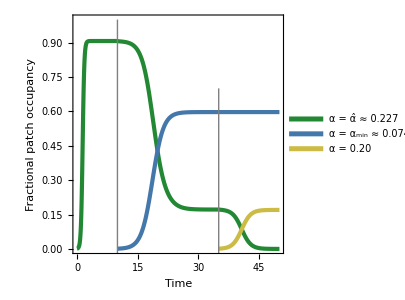

```mathematica
colors={RGBColor["#228833"],RGBColor["#4477AA"],RGBColor["#CCBB44"]};
legend={"α = α̂ ≈ 0.227","α = α_min ≈ 0.074","α = 0.20"};
Plot[Evaluate[combo[t]],{t,0,tend}, PlotRange->{0,1},
PlotStyle->Map[Directive[#,Thickness[0.01]]&,colors],
Frame->True,FrameLabel->{"Time","Fractional patch occupancy"},
PlotLegends->Placed[LineLegend[Map[Directive[#,Thickness[0.01]]&,colors],legend],{0.7,0.85}],
Epilog->{
Gray,Line[{{t2,-0.1},{t2,1}}],Line[{{t3,-0.1},{t3,0.7}}]
},
BaseStyle->Directive[FontSize->14,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],
ImageSize->{300,300},AspectRatio->1,
FrameTicks->{{Automatic, None},{Automatic,None}}
]
```

## Niche shadow plot generation (Figures 3B, 5C and D

```mathematica
FindEq[strains_, mortality_]:=Module[
{
strats=Sort[strains],
threshold=mortality,
survivors={},
freqs={},
biomasses = {},
shadowthresholds={},
invaderregion={},
shadowregion={},
c,freq,newthresh,strat
},(
Do[
c = Biomass[strats[[i]]];
If[c > threshold, (
freq = 1-Total[freqs]-mortality/c-Sum[biomasses[[j]]*freqs[[j]],{j,Length[biomasses]}]/c;
AppendTo[survivors,strats[[i]]];
AppendTo[biomasses,c];
AppendTo[freqs, freq];
strat=Strategy[Sqrt[c*threshold]];
If[strat===None,strat=alphamin];
AppendTo[invaderregion,{strat,α/.strats[[i]]}];
threshold=c^2/threshold;
AppendTo[shadowthresholds,threshold];
strat=Strategy[threshold];
If[strat===None,strat=alphamax];
AppendTo[shadowregion,{α/.strats[[i]],strat}];
strat=Strategy[threshold, True]; (* Also get high strat shadow *)
If[strat===None,Null,AppendTo[shadowregion,{strat,alphamax}]];
)];
,{i, Length[strains]}];
<|"strains"->survivors,"freqs"->freqs,"biomasses"->biomasses, "mortality" ->mortality,
"shadow_threshold"->shadowthresholds,"replaced_by"->invaderregion,"replaces"->shadowregion|>
)]
```

```mathematica
ClearAll[ShadowPlot];
ShadowPlot[status_,ymin_:0.05,ymax_:0.85]:=Module[{
x=0.02*(ymax-ymin),
tip=0.075*(ymax-ymin),
spacer=0.005*(ymax-ymin),
strains,shadows,replaced
},
(
strains=Map[Disk[{0,#},x*0.25]&,α/.status["strains"]];
shadows=Map[If[#[[1]]<ymax,Rectangle[{-x,#[[1]]},{x,Min[#[[2]],ymax]}],Nothing]&,status["replaces"]];
replaced=Map[Rectangle[{-x,Max[#[[1]],ymin]},{x,Min[ymax,#[[2]],1]}]&,status["replaced_by"]];

Show[
(* landmarks *)
Graphics[{Black, 
If[ymin===0,
{Line[{{x,0},{tip,0}}],Text["0",{tip+spacer,0},{Left,Center}]},
{Line[{{tip,ymin},{x,ymin}}],Text[ymin,{tip+spacer,ymin-spacer},{Left,Center}]}
],
If[ymax===1,
{Line[{{x,1},{tip,1}}],Text["1",{tip+spacer,1},{Left,Center}]},
{Line[{{tip,ymax},{x,ymax}}],Text[ymax,{tip+spacer,ymax+spacer},{Left,Center}]}
],
Line[{{x,alphamin},{tip,alphamin}}],Text["α_min",{tip+spacer,alphamin+spacer},{Left,Center}],
Line[{{x,alphahat},{tip,alphahat}}],Text["α̂",{tip+spacer,alphahat},{Left,Center}],
Line[{{x,alphamax},{tip,alphamax}}],Text["α_max",{tip+spacer,alphamax+spacer},{Left,Center}],
If[ymax===1,Line[{{x,1},{tip,1}}],Text["1",{tip+spacer,1},{Left,Center}],Nothing]
}],
(* shadows *)
Graphics[{RGBColor["#EE99AA"],shadows}],
(* dead by mortality *)
If[!Strategy[status["mortality"]]===None,
Graphics[{RGBColor["#777777"], 
Rectangle[{-x,ymin},{x,Strategy[status["mortality"]]}],
Rectangle[{-x,Min[ymax,Strategy[status["mortality"],True]]},{x,ymax}]}],
Graphics[]
],
(* dead by ODEs *)
Graphics[{RGBColor["#777777"], 
If[ymin<alphamin,Rectangle[{-x,ymin},{x,alphamin}],Nothing],
If[ymax>alphamax,Rectangle[{-x,alphamax},{x,ymax}],Nothing]}],
(* Number line *)
Graphics[Line[{{0,ymin},{0,ymax}}]],
If[ymax!=1,Graphics[{Dashed,Line[{{0,ymax},{0,ymax+x}}]}],Nothing],
If[ymin!=0,Graphics[{Dashed,Line[{{0,ymin},{0,ymin-x}}]}],Nothing],
(* strain dots *)
Graphics[{FaceForm[White],EdgeForm[Black],strains}],
(* Control the width *)
Graphics[Line[{{-x,ymax+1.5*x},{4*x,ymax+1.5*x}}]],

PlotStyle->FontFamily->"Arial",
PlotRange->{All,{ymin-x,ymax+2*x}},
ImageSize->{70,Automatic}
]
)]
```

### Figure 3B

```mathematica
mortality=0.5;
low = 0.05; high = 0.85;
strains={{α->alphahat}};
status=FindEq[strains,mortality];
plt1=ShadowPlot[status,low,high];
strains={{α->alphamin+0.000001},{α->alphahat}};
status=FindEq[strains,mortality];
plt2=ShadowPlot[status,low,high];
strains={{α->alphamin+0.000001},{α->0.2},{α->alphahat}};
status=FindEq[strains,mortality];
plt3=ShadowPlot[status,low,high];
GraphicsRow[{plt1,plt2,plt3}]
```

-Graphics-

### Figure S4

```mathematica
mortality = 1.5;
strains={{α->0.075},{α->0.08},{α->0.09},{α->0.1}};
status=FindEq[strains,mortality];
plt1=ShadowPlot[status,0.07,0.13];
mortality = 1.5;
strains={{α->0.075},{α->0.078},{α->0.08},{α->0.09},{α->0.1}};
status=FindEq[strains,mortality];
plt2=ShadowPlot[status,0.07,0.13];
GraphicsRow[{plt1,plt2}]
```

-Graphics-

#### Normal distribution for Figure S4

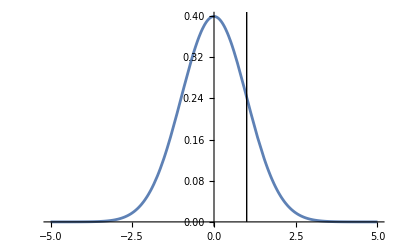

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},Epilog->Line[{{1,0},{1,0.5}}]]
```

## Figure 5C and D

```mathematica
strains={{α->alphahat}};
status=FindEq[strains,mortality]
plt1=ShadowPlot[status]
```

<|strains→{{α→0.226797}},freqs→{0.719698},biomasses→{5.35138},mortality→1.5,shadow_threshold→{19.0915},replaced_by→{{0.0860971,0.226797}},replaces→{{0.226797,0.822162}}|>

-Graphics-

```mathematica
strains={{α->alphahat},{α->0.21}};
status=FindEq[strains,mortality];
plt2=ShadowPlot[status]
```

-Graphics-

```mathematica
strains={{α->0.085}};
status=FindEq[strains,mortality];
plt3=ShadowPlot[status]
```

-Graphics-

```mathematica
strains={{α->0.085}};
status=FindEq[strains,mortality];
plt4=ShadowPlot[status,0.07,0.227]
```

-Graphics-

```mathematica
strains={{α->0.075},{α->0.085}};
status=FindEq[strains,mortality];
plt5=ShadowPlot[status,0.07,0.227]
```

-Graphics-

```mathematica
strains={{α->0.075},{α->0.085}};
status=FindEq[strains,mortality];
plt5=ShadowPlot[status,0.07,0.227]
```

-Graphics-

```mathematica
strains={{α->0.075},{α->0.08},{α->0.09},{α->0.1}};
status=FindEq[strains,mortality];
plt6=ShadowPlot[status,0.07,0.227]
```

-Graphics-

```mathematica
GraphicsRow[{plt1,plt2,plt3,plt4,plt5,plt6}]
```

-Graphics-